# “Semi-Inclusive Deep Inelastic Scattering in Wandzura-Wilczek-type approximation” S. Bastami, H. Avakian, A. V. Efremov, A. Kotzinian, B. U. Musch, B. Parsamyan, A. Prokudin, M. Schlegel, G. Schnell, P. Schweitzer, K. Tezgin, W. Vogelsang author : Alexei Prokudin, Kemal Tezgin email : prokudin@jlab.org

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/avp5627/GIT/nnpss-2018

```mathematica
<<wwsidis.m
```

Package WW-SIDIS contains the set of TMDs calculated with WW approximation and SIDIS structure functions

Copyright: Alexei Prokudin (PSU Berks), Kemal Tezgin (UConn), Version 1.01 (06/05/2018)

e-mail: prokudin@jlab.org, kemal.tezgin@uconn.edu

https://github.com/prokudin/WW-SIDIS

If you use this package, please, site arXiv for this paper and https://github.com/prokudin/WW-SIDIS

___________________________________________________________________________

Contains the following functions:

f1u[x_,Q2_ ] is the unpolarised collinear PDF for u quark, bibitem{Martin:2009iq}

f1d[x_,Q2_ ] is the unpolarised collinear PDF for d quark, bibitem{Martin:2009iq}

f1ubar[x_,Q2_ ] is the unpolarised collinear PDF for ubar quark, bibitem{Martin:2009iq}

f1dbar[x_,Q2_ ] is the unpolarised collinear PDF for dbar quark, bibitem{Martin:2009iq}

f1s[x_,Q2_ ] is the unpolarised collinear PDF for s quark, bibitem{Martin:2009iq}

f1sbar[x_,Q2_ ] is the unpolarised collinear PDF for sbar quark, bibitem{Martin:2009iq}

D1u[pion_, z_, Q2_ ] is the unpolarised collinear FF for u quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1d[pion_, z_, Q2_ ] is the unpolarised collinear FF for dbar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1ubar[pion_, z_, Q2_ ] is the unpolarised collinear FF for ubar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1dbar[pion_, z_, Q2_ ] is the unpolarised collinear FF for dbar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1s[pion_, z_, Q2_ ] is the unpolarised collinear FF for s quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1sbar[pion_, z_, Q2_ ] is the unpolarised collinear FF for sbar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

g1u[x_,Q2_ ] is the helicity collinear PDF for u quark, bibitem{Gluck:1998xa}

g1d[x_,Q2_ ] is the helicity collinear PDF for d quark, bibitem{Gluck:1998xa}

g1ubar[x_,Q2_ ] is the helicity collinear PDF for ubar quark, bibitem{Gluck:1998xa}

g1dbar[x_,Q2_ ] is the helicity collinear PDF for dbar quark, bibitem{Gluck:1998xa}

g1s[x_,Q2_ ] is the helicity collinear PDF for s quark, bibitem{Gluck:1998xa}

g1sbar[x_,Q2_ ] is the helicity collinear PDF for sbar quark, bibitem{Gluck:1998xa}

h1u[x_,Q2_ ] is the transversity collinear PDF for u quark, bibitem{Anselmino:2013vqa}

h1d[x_,Q2_ ] is the transversity collinear PDF for d quark, bibitem{Anselmino:2013vqa}

h1ubar[x_,Q2_ ] is the transversity collinear PDF for ubar quark, bibitem{Anselmino:2013vqa}

h1dbar[x_,Q2_ ] is the transversity collinear PDF for dbar quark, bibitem{Anselmino:2013vqa}

h1s[x_,Q2_ ] is the transversity collinear PDF for s quark, bibitem{Anselmino:2013vqa}

h1sbar[x_,Q2_ ] is the transversity collinear PDF for sbar quark, bibitem{Anselmino:2013vqa}

H1perpFirstMoment[quark_, pion_, x_, Q2_] the first moment of Collins FF favoured, bibitem{Anselmino:2013vqa}

f1TperpuFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for u quark, bibitem{Anselmino:2011gs}

f1TperpdFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for d quark, bibitem{Anselmino:2011gs}

f1TperpubarFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for ubar quark, bibitem{Anselmino:2011gs}

f1TperpdbarFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for dbar quark, bibitem{Anselmino:2011gs}

f1TperpsFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for s quark, bibitem{Anselmino:2011gs}

f1TperpsbarFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for sbar quark, bibitem{Anselmino:2011gs}

h1TperpuSecondMoment[x_,Q2_] the second moment of pretzelosity for u quark, bibitem{Lefky:2014eia};

h1TperpdSecondMoment[x_,Q2_] the second moment of pretzelosity for d quark, bibitem{Lefky:2014eia};

h1perpuFirstMoment[x_,Q2_] the first moment of Boer-Mulders function for u quark, bibitem{Barone:2009hw};

h1perpdFirstMoment[x_,Q2_] the first moment of Boer-Mulders function for d quark, bibitem{Barone:2009hw};

h1Lu[x_,Q2_ ] is the h_(1  L)^⊥ PDF for u quark, this work

h1Ld[x_,Q2_ ] is the h_(1  L)^⊥ PDF for u quark, this work

g1Tperpu[x_,Q2_ ] is the g_(1  T)^⊥ PDF for u quark, this work

g1Tperpd[x_,Q2_ ] is the g_(1  T)^⊥ PDF for d quark, this work

ALL[pion_, x_, z_, Q2_, PT_] is the A_LL asymmetry

AUTSivers[pion_, x_, z_, Q2_, PT_] is the Sivers A_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AUTCollins[pion_, x_, z_, Q2_, PT_] is the Collins A_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] + SubscriptBox[Φ, S]]) asymmetry

AUTh1tp[pion_, x_, z_, Q2_, PT_] is the Pretzelosity A_UT^(TraditionalForm`sin[3\ SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AUUcos2phi[pion_, x_, z_, Q2_, PT_] is the Boer-Mulders A_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]]) asymmetry

ALT[pion_, x_, z_, Q2_, PT_] is the Double Spin A_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AULsin2phi[pion_, x_, z_, Q2_, PT_] is the Kotzinian-Mulders A_UL^(TraditionalForm`sin[2 SubscriptBox[Φ, h]]) asymmetry

ALTcosPhi[pion_, x_, z_, Q2_, PT_] is the A_LT^(TraditionalForm`cos[SubscriptBox[Φ, S]]) asymmetry

AULsinphi[pion_, x_, z_, Q2_, PT_] is the A_UL^(TraditionalForm`sin[SubscriptBox[Φ, h]]) asymmetry

ALLcosphi[pion_, x_, z_, Q2_, PT_] is the A_LL^(TraditionalForm`cos[SubscriptBox[Φ, h]]) asymmetry

ALTcos2PhiminusPhiS[pion_, x_, z_, Q2_, PT_] is the A_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AUUcosphi[pion_, x_, z_, Q2_, PT_] is the A_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]]) asymmetry

AUTsinphiS[pion_, x_, z_, Q2_, PT_] is the A_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]]) asymmetry

AUTsin2PhiminusPhiS[pion_, x_, z_, Q2_, PT_] is the A_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

Semi-Inclusive Deep Inelastic Cross Section, CrossSection[pion_,x_,z_,Q2_,PT_,energy_,phih_,phiS_,helicity_,targetpolarization_] calculates the differential cross section of specified pion_,x_,z_,Q2_,PT_,energy_,phih_,phiS_,helicity_,targetpolarization_

Contains the following constants:

avp unpolarized D_1 TMD fragmentation distribution width

avk unpolarized f_1 TMD  width

avkg helicity g_1TMD width

avks f_(1  T)^⊥ (Sivers function) TMD width

avkh H_1^⊥ (Collins fragmentation function) TMD width

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

PDF grid read from Grids/mstw2008lo.00.dat

Unpolarized parton distribution functions:

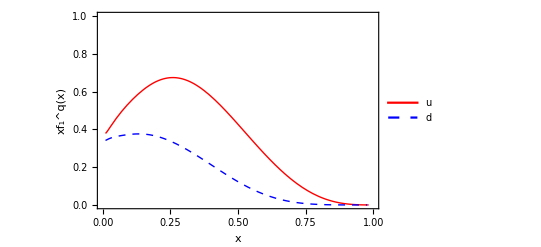

```mathematica
Plot[{x f1u[x,2.4],x f1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","xf_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

Sivers parton distribution functions:

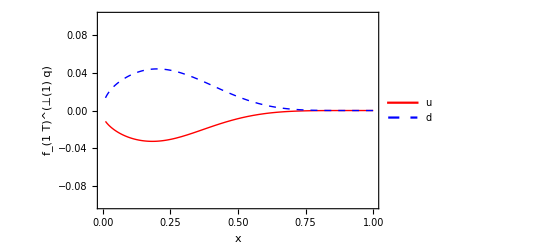

```mathematica
Plot[{x f1TperpuFirstMoment[x,2.4],x f1TperpdFirstMoment[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.1,0.1}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","f_(1  T)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d"},{0.7,0.7}]]
```

Sivers asymmetry:

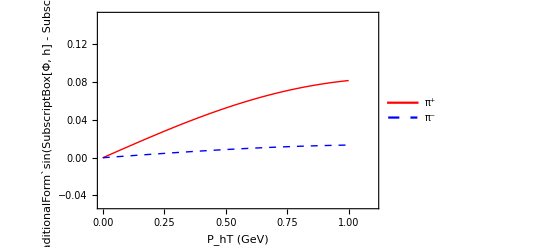

```mathematica
Plot[{AUTSivers["pi+",0.1,0.34,2.4, PT],AUTSivers["pi-",0.1,0.34,2.4, PT]},{PT,0,1.},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1.1},{-0.05,0.15}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"P_hT (GeV)","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.85}]]
```